# Wolfram Challenges Benchmark

Interactive driver for the ChallengesBenchmark paclet. This notebook is equivalent to scripts/RunBenchmark.wls but with a live dashboard and an analysis section you can re-run cell by cell.

## 1. Load the paclet

Assumes this notebook lives at the repo root. Re-run this cell whenever you edit a package file.

```mathematica
SetDirectory[NotebookDirectory[]];
PrependTo[$Path, NotebookDirectory[]];
Get[FileNameJoin[{NotebookDirectory[], "ChallengesBenchmark", "ChallengesBenchmark.wl"}]];
```

```mathematica
?ChallengesBenchmark`*
```

## 2. Configure the run

Edit the following association. Any option left out falls back to $BenchmarkDefaults.

```mathematica
config = <|
  "ChallengesPath"   -> FileNameJoin[{NotebookDirectory[], "ChallengesTestDataV1.json"}],
  "TestBankPath"     -> FileNameJoin[{NotebookDirectory[], "ChallengesTests.wxf"}],
  "SolutionsDir"     -> FileNameJoin[{NotebookDirectory[], "solutions", "claude-opus-4.6"}],
  "Model"            -> "claude-opus-4.6",
  "OutputDirectory"  -> FileNameJoin[{NotebookDirectory[], "runs"}],
  "TimeConstraint"   -> 60,
  "MemoryConstraint" -> 2*^9,
  "Parallel"         -> Automatic,
  "IsolationMode"    -> "PerTestKernel",
  "Filter"           -> All
|>;
```

Quick sanity check — drop to a small filter like {"Aliquot", "FizzBuzz"} while iterating.

```mathematica
config = <|
  "ChallengesPath"   -> FileNameJoin[{NotebookDirectory[], "ChallengesTestDataV1.json"}],
  "TestBankPath"     -> FileNameJoin[{NotebookDirectory[], "ChallengesTests.wxf"}],
  "SolutionsDir"     -> FileNameJoin[{NotebookDirectory[], "solutions", "claude-opus-4.6"}],
  "Model"            -> "claude-opus-4.6",
  "OutputDirectory"  -> FileNameJoin[{NotebookDirectory[], "runs"}],
  "TimeConstraint"   -> 60,
  "MemoryConstraint" -> 2*^9,
  "Parallel"         -> Automatic,
  "IsolationMode"    -> "PerTestKernel",
  "Filter"->{"AliquotSequence","FizzBuzz","AnagramWords","AscendingSublists"}
|>;
```

## 3. Load inputs

```mathematica
challenges = ChallengesBenchmark`LoadChallenges[config["ChallengesPath"]];
testBank   = ChallengesBenchmark`LoadTestBank[config["TestBankPath"]];
solutions  = ChallengesBenchmark`LoadSolutions[config["SolutionsDir"]];

<|"challenges" -> Length[challenges],
  "testBank"   -> Total[Length /@ Values[testBank]],
  "solutions"  -> Length[solutions]|>
```

<|challenges→166,testBank→724,solutions→166|>

```mathematica
challenges[[1]]
```

<|index→1,name→AliquotSequence,instruction→Write Wolfram Language code that performs the following task,prompt→Define AliquotSequence[n] returning the aliquot sequence starting at n,
terminating once it reaches 1 or enters a cycle.|>

```mathematica
testBank[[1]]//Dataset
```

```mathematica
solutions[[1]]
```

<|code→AliquotSequence[num_Integer?Positive] := Module[{seq = {num}, next, seen},
  seen = Association[num -> True];
  Do[
    next = DivisorSigma[1, Last[seq]] - Last[seq];
    If[KeyExistsQ[seen, next] || Last[seq] == 1, Break[]];
    AppendTo[seq, next];
    seen[next] = True,
    {99}
  ];
  seq
],metadata→<|model→claude-opus-4.6,challengeName→AliquotSequence,sourceHash→sha256:def85cc1d50f8590b47400ed1fe25175fdbdad1e2aa6910ebde1c3d9097a0734,generatedAt→2026-04-19T21:08:12,extractor→ExtractCode/v1|>|>

## 4. Run the benchmark

This call blocks until all tests finish. Progress is streamed to runs/<runId>/progress.jsonl — the dashboard in the next section tails it live.

```mathematica
run = ChallengesBenchmark`RunBenchmark[
  challenges, testBank, solutions,
  "Model"            -> config["Model"],
  "OutputDirectory"  -> config["OutputDirectory"],
  "TimeConstraint"   -> config["TimeConstraint"],
  "MemoryConstraint" -> config["MemoryConstraint"],
  "Parallel"         -> config["Parallel"],
  "IsolationMode"    -> config["IsolationMode"],
  "Filter"           -> config["Filter"]
];

<|"runId" -> run["runId"],
  "runDir" -> run["runDir"],
  "summary" -> run["meta", "summary"]|>
```

[2026-04-19T20:28:39] [Info] RunBenchmark: model=claude-opus-4.6 runId=run-ISODateTimeHyphenated-e87c90 tests=724 parallel=15 mode=PerTestKernel
[2026-04-19T20:54:21] [Info] RunBenchmark complete: run-ISODateTimeHyphenated-e87c90 (passed 464 / 724)

Part::partw: Part 1 of {} does not exist.

First::normal: Nonatomic expression expected at position 1 in First[2].

First::normal: Nonatomic expression expected at position 1 in First[1].

Part::partd: Part specification {Null,{}}⟦1,2⟧ is longer than depth of object.

Do::nliter: Nonlist iterator Lookup[assoc$7552504,c2$7552504,{}] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Do::nliter will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

First::normal: Nonatomic expression expected at position 1 in First[2].

First::normal: Nonatomic expression expected at position 1 in First[1].

Part::partd: Part specification {Null,{}}⟦1,2⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

First::normal: Nonatomic expression expected at position 1 in First[2].

First::normal: Nonatomic expression expected at position 1 in First[1].

Part::partd: Part specification {Null,{}}⟦1,2⟧ is longer than depth of object.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Part::take: Cannot take positions 2 through -1 in {}.

Take::take: Cannot take positions 1 through 2 in {{1,0}}.

Thread::tdlen: Objects of unequal length in {0,0}+{{1,0}} cannot be combined.

Thread::tdlen: Objects of unequal length in 2+{{1,0}}+{0,0} cannot be combined.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{0,0},{{1,0}}+{0,0},2+{{1,0}}+{0,0}].

Take::take: Cannot take positions 1 through 13 in {{1,0},{0,1},{-1,0},{0,-1}}.

MapThread::mptd: Object Take[{{1,0},{0,1},{-1,0},{0,-1}},13] at position {2, 1} in MapThread[ConstantArray,{Take[{{1,0},{0,1},{-1,0},{0,-1}},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}] has only 0 of required 1 dimensions.

Take::take: Cannot take positions 1 through 25 in MapThread[ConstantArray,{Take[{{1,0},{0,1},{-1,0},{0,-1}},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}].

MapThread::mptd: Object Take[{{1,0},{0,1},{-1,0},{0,-1}},13] at position {2, 1} in MapThread[ConstantArray,{Take[{{1,0},{0,1},{-1,0},{0,-1}},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{0,0},{MapThread[ConstantArray,{Take[{{«2»},{«2»},{«2»},{«2»}},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}],MapThread[ConstantArray,{Take[{{«2»},{«2»},{«2»},{«2»}},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}]},{25+MapThread[ConstantArray,{Take[{«4»},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}],25+MapThread[ConstantArray,{Take[{«4»},13],{1,1,2,2,3,3,4,4,5,5,6,6,7}}]}].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B},k].

StringJoin::string: String expected at position 1 in Take[{A,B},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A,B},k]<>A,-Min[1,1+k]].

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B},k]<>A,-Min[1,1+k]]].

Range::range: Range specification in Range[Min[1,StringLength[StringTake[Take[{«2»},k]<>A,-Min[1,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[StringTake[Take[{A,B},k]<>A,-Min[1,1+k]],-Min[1,StringLength[StringTake[Take[«2»]<>A,-Min[«2»]]]]].

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[AB,Min[1,StringLength[StringTake[Take[{«2»},k]<>A,-Min[1,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B},k].

StringJoin::string: String expected at position 1 in Take[{A,B},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A,B},k]<>A,-Min[1,1+k]].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B},k]<>A,-Min[1,1+k]]].

Range::range: Range specification in Range[Min[1,StringLength[StringTake[Take[{«2»},k]<>A,-Min[1,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[AB,Min[1,StringLength[StringTake[Take[{«2»},k]<>A,-Min[1,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B},k].

General::stop: Further output of Take::seqs will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in Take[{A,B},k]<>A.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B},k]<>A,-Min[1,1+k]]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

Range::range: Range specification in Range[Min[1,StringLength[StringTake[Take[{«2»},k]<>A,-Min[1,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[AB,Min[1,StringLength[StringTake[Take[{«2»},k]<>A,-Min[1,Plus[«2»]]]]]].

General::stop: Further output of StringTake::mseqs will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B,A},k].

StringJoin::string: String expected at position 1 in Take[{A,B,A},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A,B,A},k]<>A,-Min[2,1+k]].

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B,A},k]<>A,-Min[2,1+k]]].

Range::range: Range specification in Range[Min[2,StringLength[StringTake[Take[{«3»},k]<>A,-Min[2,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[StringTake[Take[{A,B,A},k]<>A,-Min[2,1+k]],-Min[2,StringLength[StringTake[Take[«2»]<>A,-Min[«2»]]]]].

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[ABA,Min[2,StringLength[StringTake[Take[{«3»},k]<>A,-Min[2,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B,A},k].

StringJoin::string: String expected at position 1 in Take[{A,B,A},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A,B,A},k]<>A,-Min[2,1+k]].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B,A},k]<>A,-Min[2,1+k]]].

Range::range: Range specification in Range[Min[2,StringLength[StringTake[Take[{«3»},k]<>A,-Min[2,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[ABA,Min[2,StringLength[StringTake[Take[{«3»},k]<>A,-Min[2,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B,A},k].

General::stop: Further output of Take::seqs will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in Take[{A,B,A},k]<>A.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B,A},k]<>A,-Min[2,1+k]]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

Range::range: Range specification in Range[Min[2,StringLength[StringTake[Take[{«3»},k]<>A,-Min[2,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[ABA,Min[2,StringLength[StringTake[Take[{«3»},k]<>A,-Min[2,Plus[«2»]]]]]].

General::stop: Further output of StringTake::mseqs will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A},k].

StringJoin::string: String expected at position 1 in Take[{A},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A},k]<>A,-Min[0,1+k]].

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A},k]<>A,-Min[0,1+k]]].

Range::range: Range specification in Range[Min[0,StringLength[StringTake[Take[{«1»},k]<>A,-Min[0,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[StringTake[Take[{A},k]<>A,-Min[0,1+k]],-Min[0,StringLength[StringTake[Take[«2»]<>A,-Min[«2»]]]]].

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[A,Min[0,StringLength[StringTake[Take[{«1»},k]<>A,-Min[0,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A},k].

StringJoin::string: String expected at position 1 in Take[{A},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A},k]<>A,-Min[0,1+k]].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A},k]<>A,-Min[0,1+k]]].

Range::range: Range specification in Range[Min[0,StringLength[StringTake[Take[{«1»},k]<>A,-Min[0,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[A,Min[0,StringLength[StringTake[Take[{«1»},k]<>A,-Min[0,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A},k].

General::stop: Further output of Take::seqs will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in Take[{A},k]<>A.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A},k]<>A,-Min[0,1+k]]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

Range::range: Range specification in Range[Min[0,StringLength[StringTake[Take[{«1»},k]<>A,-Min[0,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[A,Min[0,StringLength[StringTake[Take[{«1»},k]<>A,-Min[0,Plus[«2»]]]]]].

General::stop: Further output of StringTake::mseqs will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B,A,B},k].

StringJoin::string: String expected at position 1 in Take[{A,B,A,B},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A,B,A,B},k]<>A,-Min[3,1+k]].

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B,A,B},k]<>A,-Min[3,1+k]]].

Range::range: Range specification in Range[Min[3,StringLength[StringTake[Take[{«4»},k]<>A,-Min[3,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[StringTake[Take[{A,B,A,B},k]<>A,-Min[3,1+k]],-Min[3,StringLength[StringTake[Take[«2»]<>A,-Min[«2»]]]]].

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[ABAB,Min[3,StringLength[StringTake[Take[{«4»},k]<>A,-Min[3,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B,A,B},k].

StringJoin::string: String expected at position 1 in Take[{A,B,A,B},k]<>A.

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[Take[{A,B,A,B},k]<>A,-Min[3,1+k]].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B,A,B},k]<>A,-Min[3,1+k]]].

Range::range: Range specification in Range[Min[3,StringLength[StringTake[Take[{«4»},k]<>A,-Min[3,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[ABAB,Min[3,StringLength[StringTake[Take[{«4»},k]<>A,-Min[3,Plus[«2»]]]]]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{A,B,A,B},k].

General::stop: Further output of Take::seqs will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in Take[{A,B,A,B},k]<>A.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[StringTake[Take[{A,B,A,B},k]<>A,-Min[3,1+k]]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

Range::range: Range specification in Range[Min[3,StringLength[StringTake[Take[{«4»},k]<>A,-Min[3,Plus[«2»]]]]],0,-1] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

StringTake::mseqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) or a list of sequence specifications expected at position 2 in StringTake[ABAB,Min[3,StringLength[StringTake[Take[{«4»},k]<>A,-Min[3,Plus[«2»]]]]]].

General::stop: Further output of StringTake::mseqs will be suppressed during this calculation.

Function::slotn: Slot number 2 in pairV$7777317[#2]==0& cannot be filled from (pairV$7777317[#2]==0&)[6].

Function::slotn: Slot number 2 in pairV$7777317[#2]==0& cannot be filled from (pairV$7777317[#2]==0&)[5].

Function::slotn: Slot number 2 in pairV$7777317[#2]==0& cannot be filled from (pairV$7777317[#2]==0&)[4].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in pairV$7777390[#2]==0& cannot be filled from (pairV$7777390[#2]==0&)[2].

Function::slotn: Slot number 2 in pairV$7777390[#2]==0& cannot be filled from (pairV$7777390[#2]==0&)[4].

Function::slotn: Slot number 2 in pairV$7777390[#2]==0& cannot be filled from (pairV$7777390[#2]==0&)[3].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in pairV$7777455[#2]==0& cannot be filled from (pairV$7777455[#2]==0&)[2].

Function::slotn: Slot number 2 in pairV$7777505[#2]==0& cannot be filled from (pairV$7777505[#2]==0&)[4].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in pairV$7777570[#2]==0& cannot be filled from (pairV$7777570[#2]==0&)[3].

Function::slotn: Slot number 2 in pairV$7777570[#2]==0& cannot be filled from (pairV$7777570[#2]==0&)[8].

Function::slotn: Slot number 2 in pairV$7777570[#2]==0& cannot be filled from (pairV$7777570[#2]==0&)[15].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in pairV$7777638[#2]==0& cannot be filled from (pairV$7777638[#2]==0&)[2].

Function::slotn: Slot number 2 in pairV$7777638[#2]==0& cannot be filled from (pairV$7777638[#2]==0&)[7].

Function::slotn: Slot number 2 in pairV$7777638[#2]==0& cannot be filled from (pairV$7777638[#2]==0&)[9].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in pairV$7777703[#2]==0& cannot be filled from (pairV$7777703[#2]==0&)[19].

Function::slotn: Slot number 2 in pairV$7777703[#2]==0& cannot be filled from (pairV$7777703[#2]==0&)[22].

Function::slotn: Slot number 2 in pairV$7777703[#2]==0& cannot be filled from (pairV$7777703[#2]==0&)[32].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Table::write: Tag List in {{0},{1},{2}} is Protected.

Table::iterb: Iterator {Table[Append[{{0},{1},{2}},d],{{{0},{1},{2}},{{0},{1},{2}}},{d,DeleteCases[{0,1,2},Last[{{«1»},{«1»},{«1»}}]]}],Table[Append[{{0},{1},{2}},d],{{{0},{1},{2}},{{0},{1},{2}}},{d,DeleteCases[{0,1,2},Last[{{«1»},{«1»},{«1»}}]]}]} does not have appropriate bounds.

Part::partw: Part 21 of {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} does not exist.

Set::span: 2;;Min[20,1+{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦21⟧] is not a valid Span specification. A Span specification should be 1, 2 or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 51 of {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} does not exist.

Set::span: 2;;Min[50,1+{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦51⟧] is not a valid Span specification. A Span specification should be 1, 2 or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

StringLength::string: String expected at position 1 in StringLength[sym].

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[sym,1].

StringDrop::strse: A string or list of strings is expected at position 1 in StringDrop[sym,1].

StringJoin::string: String expected at position 1 in ToUpperCase[StringTake[sym,1]]<>StringDrop[sym,1].

StringJoin::string: String expected at position 2 in ToUpperCase[StringTake[sym,1]]<>StringDrop[sym,1].

Function::slotn: Slot number 2 in !used$7860956⟦#2⟧& cannot be filled from (!used$7860956⟦#2⟧&)[1].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7860956⟦#2⟧& cannot be filled from (!used$7860956⟦#2⟧&)[6].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7860956⟦#2⟧& cannot be filled from (!used$7860956⟦#2⟧&)[13].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Function::slotn: Slot number 2 in !used$7862771⟦#2⟧& cannot be filled from (!used$7862771⟦#2⟧&)[2].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7862771⟦#2⟧& cannot be filled from (!used$7862771⟦#2⟧&)[9].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7862771⟦#2⟧& cannot be filled from (!used$7862771⟦#2⟧&)[3].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Function::slotn: Slot number 2 in !used$7863620⟦#2⟧& cannot be filled from (!used$7863620⟦#2⟧&)[1].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7863620⟦#2⟧& cannot be filled from (!used$7863620⟦#2⟧&)[6].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7863620⟦#2⟧& cannot be filled from (!used$7863620⟦#2⟧&)[13].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Function::slotn: Slot number 2 in !used$7863962⟦#2⟧& cannot be filled from (!used$7863962⟦#2⟧&)[1].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7863962⟦#2⟧& cannot be filled from (!used$7863962⟦#2⟧&)[6].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7863962⟦#2⟧& cannot be filled from (!used$7863962⟦#2⟧&)[13].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Function::slotn: Slot number 2 in !used$7864213⟦#2⟧& cannot be filled from (!used$7864213⟦#2⟧&)[2].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7864213⟦#2⟧& cannot be filled from (!used$7864213⟦#2⟧&)[9].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Function::slotn: Slot number 2 in !used$7864213⟦#2⟧& cannot be filled from (!used$7864213⟦#2⟧&)[18].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Prepend::argt: Prepend called with 3 arguments; 1 or 2 arguments are expected.

Prepend::argt: Prepend called with 4 arguments; 1 or 2 arguments are expected.

Prepend::argt: Prepend called with 5 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Prepend::argt will be suppressed during this calculation.

Prepend::argt: Prepend called with 8 arguments; 1 or 2 arguments are expected.

Prepend::argt: Prepend called with 5 arguments; 1 or 2 arguments are expected.

Prepend::argt: Prepend called with 6 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Prepend::argt will be suppressed during this calculation.

Prepend::argt: Prepend called with 3 arguments; 1 or 2 arguments are expected.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[25,Prepend[Prepend[{},1,1]]].

Prepend::argt: Prepend called with 4 arguments; 1 or 2 arguments are expected.

Prepend::argt: Prepend called with 8 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Prepend::argt will be suppressed during this calculation.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[10,Prepend[{},1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1]].

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Function::slotn: Slot number 2 in #1==#2& cannot be filled from (#1==#2&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Table::nliter: Nonlist iterator With[{r=5-3 b},If[EvenQ[r],{a=Quotient[r,2]},Sequence@@{}]] at position 3 does not evaluate to a real numeric value.

Function::slotn: Slot number 2 in OrderedQ[{Length[#1],#1},{Length[#2],#2}]& cannot be filled from (OrderedQ[{Length[#1],#1},{Length[#2],#2}]&)[{b,0,1}].

Table::nliter: Nonlist iterator With[{r=14-3 b},If[EvenQ[r],{a=Quotient[r,2]},Sequence@@{}]] at position 3 does not evaluate to a real numeric value.

Function::slotn: Slot number 2 in OrderedQ[{Length[#1],#1},{Length[#2],#2}]& cannot be filled from (OrderedQ[{Length[#1],#1},{Length[#2],#2}]&)[{b,0,4}].

Table::nliter: Nonlist iterator With[{r=3-3 b},If[EvenQ[r],{a=Quotient[r,2]},Sequence@@{}]] at position 3 does not evaluate to a real numeric value.

Function::slotn: Slot number 2 in OrderedQ[{Length[#1],#1},{Length[#2],#2}]& cannot be filled from (OrderedQ[{Length[#1],#1},{Length[#2],#2}]&)[{b,0,1}].

Table::nliter: Nonlist iterator With[{r=6-3 b},If[EvenQ[r],{a=Quotient[r,2]},Sequence@@{}]] at position 3 does not evaluate to a real numeric value.

Function::slotn: Slot number 2 in OrderedQ[{Length[#1],#1},{Length[#2],#2}]& cannot be filled from (OrderedQ[{Length[#1],#1},{Length[#2],#2}]&)[{b,0,2}].

Table::nliter: Nonlist iterator With[{r=19-3 b},If[EvenQ[r],{a=Quotient[r,2]},Sequence@@{}]] at position 3 does not evaluate to a real numeric value.

Function::slotn: Slot number 2 in OrderedQ[{Length[#1],#1},{Length[#2],#2}]& cannot be filled from (OrderedQ[{Length[#1],#1},{Length[#2],#2}]&)[{b,0,6}].

Part::partd: Part specification t⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification t⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification t⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{1,3}}+{0,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {{1,3,0},{1,0,1}}+{0,-1,-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {{1,1}}+{0,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {{1,3,2},{1,0,2}}+{0,-1,-2} cannot be combined.

Sort::normal: Nonatomic expression expected at position 1 in Sort[StringJoin].

CellularAutomaton::inite: The initial condition specification {0,1,0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 do not have head List.

CellularAutomaton::kspec: Since position 1 of rule specification {0,1,0} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1} or {k, wts}, where k is a machine integer > 1 and wts is a nonempty array of non-negative machine integers.

Part::partd: Part specification CellularAutomaton[{0,1,0},5]⟦All,2⟧ is longer than depth of object.

CellularAutomaton::inite: The initial condition specification {0,0,1,0,0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 do not have head List.

CellularAutomaton::nspec: If rule specification {0,0,1,0,0} is a List that is not a list of rules, it must have between 2 and 4 elements.

Part::partd: Part specification CellularAutomaton[{0,0,1,0,0},5]⟦All,3⟧ is longer than depth of object.

CellularAutomaton::inite: The initial condition specification {0,0,0,1,0,0,0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 do not have head List.

General::stop: Further output of CellularAutomaton::inite will be suppressed during this calculation.

CellularAutomaton::nspec: If rule specification {0,0,0,1,0,0,0} is a List that is not a list of rules, it must have between 2 and 4 elements.

Part::partd: Part specification CellularAutomaton[{0,0,0,1,0,0,0},5]⟦All,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

CellularAutomaton::nspec: If rule specification {0,0,0,0,1,0,0,0,0} is a List that is not a list of rules, it must have between 2 and 4 elements.

General::stop: Further output of CellularAutomaton::nspec will be suppressed during this calculation.

Sort::normal: Nonatomic expression expected at position 1 in Sort[All].

SetDelayed::write: Tag MaxColorDistance in MaxColorDistance[img_Image] is Protected.

LessEqual::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

General::stop: Further output of LessEqual::meprec will be suppressed during this calculation.

LessEqual::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1 - Divide[-((1 + <<6>> - Divide[2 <<1>> ((-Power[2, <<1>>] + Divide[1 + Power[3, <<1>>], 2 Power[2, <<1>>]]) (-5 + <<4>> - Divide[<<2>>]) + <<1>>), <<1>>]) <<1>>) + <<1>>, <<1>>].

General::stop: Further output of LessEqual::meprec will be suppressed during this calculation.

Coefficient::ivar: 1 is not a valid variable.

<|runId→run-ISODateTimeHyphenated-e87c90,runDir→/Users/jofree/Documents/Claude/Projects/WolframChallengesBenchmark/runs/run-ISODateTimeHyphenated-e87c90,summary→<|total→724,passed→464,failed→220,evaluationError→3,timedOut→10,memoryExceeded→5,parseError→22,noSolution→0,kernelDied→0,passRate→0.640884,challengesAttempted→166,challengesFullyPassing→87,perChallenge→<|AliquotSequence→1,AllParentheticalExpressions→0,AlmostPalindromes→1,AlmostRepeatingPrimes→1,AnagramWords→1,AnglesOfA3DTriangle→1,AntipodalCity→0,AntipodeAboveOrBelowSeaLevel→1,AscendingSublists→1,AverageElevation→0,BabbageSquares→0,BalancedTernary→0,BasebPalindromicNumbers→1,BreakingTheCaesarCipher→1,BubbleSort→0,ButterfliedStrings→1,CapitalCitiesNearALatitude→0,CarryCounting→1,CellularAutomaton→1,CellularAutomatonTransients→1,ColorConversion→0,CombineNOnes→0,CompositeNumber→0,ConstantDigitSum→1,CountingLatticePaths→1,CountingTwinPrimePairs→1,CountPalindromicSubstrings→1,CountryChains→0,CountTheNumberOfSquares→0,DeriffleAList→0,DiagonalsOfRule30→0,DigitalClockArithmetic→0,DigitalRoot→1,DigitFrequencyForPi→0,DiscreteSpiral→0,EmirpsIsPrimesBackward→1,FactorialDigitFrequency→1,FactorialZeros→1,FactorTrees→0,FarthestWords→0,FewestNumberOfCoins→1,FindGoldbachPartitions→1,FindingFlipPrimes→0,FiveLongWeekendsInAMonth→0,FivePointConic→0,FizzBuzz→1,Flutter→1,ForbiddenSubstrings→0,FourPileNim→1,FourPointParabola→0,FridayThe13thsInAYear→1,GettingABasketballScore→0,GrayCode→1,GrayscaleSpectrum→1,HashLoop→0,HowRoundIsACountry→0,IntegerNameLengths→0,IntegersWithGivenDigitSums→0,IteratedRomanNumeralization→0,JosephusProblem→1,KnightPoints→0,LargeIntegersMod2027→0,LatticePointsInASphere→1,LengthOfTheCollatzSequence→1,LetterBank→0,ListifyTheElementsOfAList→1,ListPrimePalindromes→1,LongestGraphCycle→0,LongestReversedSequence→1,LookAndSaySequence→1,MagicSquares→1,MakingChange→1,MaximalContiguousSum→1,MaximumColorDistance→0,MaximumOverhang→0,MaximumRomanNumeralLength→1,MinimalCellularAutomaton→0,MirrorMirror→0,MostDistinctLetters→1,MostOccurringWeekdaysInAYear→1,MostRomanNumerals→1,MostWeekendBirthdays→1,MultiplesOf3And5→1,MultiplicationTable→1,NDimensionalQueenGraph→0,NearestNumbers→1,NextPermutation→1,NextTermOfALookAndSaySequence→0,NormalFormOfAPlane→1,NumberOfVowels→0,NumberTriangles→0,OddsBeforeEvens→1,OneFingerDistance→1,OnTheCriticalLine→0,OverlappingSequences→0,PairingCompatibleIntegers→0,Pairingfunction→1,PairsThatSumTo100→0,PalindromeFromAWord→1,Palindromes→1,PalindromicRomanNumerals→1,PancakeScramble→1,PancakeScramblePeriod→0,PartitionsOfIncreasingLength→1,PermutationCount→1,PermutationIndex→0,PigLatin→1,PlanesInSpace→0,PointInsideTriangle→1,PolygonBilliards→0,PowerfulDigitFrequencies→1,PrimeBase→0,PrimeFibonacciNumbers→1,PrimeGaps→0,PrimePalindromePi→1,PrimePowerPi→0,PureFunctionMaker→0,PythagoreanPrimes→1,QuadrilateralMidpoints→1,RATSSequences→1,ReasonablyCloseRectangle→0,RemoveIdenticalNeighbors→0,RemoveRepeatedCharacters→1,RepeatFreeTernarySequences→0,ReplicateCharactersInAString→1,ReverseEachWord→0,RollingPolygonHeight→0,RomanNumeralsVersusDecimal→1,RomanSubstitutionWords→0,Rotodromes→0,RoughGoldbachSplits→1,SeparateOnesByZeros→1,SequenceHuntInPi→1,ShortestWordFromSomeLetters→1,ShortestWordLadder→1,SilvermansSequence→0,SingleDigitNumbers→1,SmallestWordNumber→0,SmallFactorsOfLargeNumbers→0,SpellWithChemicalElements→0,SquarefreeTernarySequences→1,SquareRootFloorDigits→1,SquareRootOfTwoViaPell→1,SquareSequences→0,SquareSum→1,StartAndEndOfABigNumber→0,SteinerInellipse→0,SumsToAnInteger→0,SwitchTheCase→1,TelephoneWords→0,TestingIfListsAreShuffled→1,TexasSharpshooter→0,TheBombProblem→0,TheMcnuggetProblem→1,ThreeTriangularNumbers→0,UpAndDownWords→0,ValidIntegerTriangle→1,ValidParentheses→0,VigenereCipher→0,WaterInABarrel→1,WordFromLetterSum→1,WordsBeginningAndEndingWithAGivenLetter→0,WordsFromWords→0,WordsWithAGivenPrefix→1,WriteInMorseCode→0,ZigzagNumbers→1|>,fastest→{<|testId→FactorTrees/1,durationSec→0.|>,<|testId→FactorTrees/2,durationSec→0.|>,<|testId→FactorTrees/3,durationSec→0.|>,<|testId→FactorTrees/4,durationSec→0.|>,<|testId→FactorTrees/5,durationSec→0.|>},slowest→{<|testId→ThreeTriangularNumbers/3,durationSec→60.136171|>,<|testId→ThreeTriangularNumbers/2,durationSec→60.09772|>,<|testId→ThreeTriangularNumbers/1,durationSec→60.072328|>,<|testId→PancakeScramblePeriod/4,durationSec→60.005083|>,<|testId→PancakeScramblePeriod/5,durationSec→60.004969|>}|>|>

## 5. Live dashboard

LiveDashboard polls progress.jsonl. Evaluate this cell while a run is happening in another kernel, or after the run to review the final state.

```mathematica
ChallengesBenchmark`LiveDashboard[run["runDir"]]
```

## 6. Write the report

```mathematica
reportPaths = ChallengesBenchmark`WriteReport[run, run["runDir"]];
SystemOpen[reportPaths["html"]];
reportPaths
```

<|html→/private/var/folders/c_/k0rk9m2x6cd9jxt0k9xqsg9m0000gn/T/m001834617561/run-ISODateTimeHyphenated-390b1c/report.html,markdown→/private/var/folders/c_/k0rk9m2x6cd9jxt0k9xqsg9m0000gn/T/m001834617561/run-ISODateTimeHyphenated-390b1c/report.md,json→/private/var/folders/c_/k0rk9m2x6cd9jxt0k9xqsg9m0000gn/T/m001834617561/run-ISODateTimeHyphenated-390b1c/report.json,junit→/private/var/folders/c_/k0rk9m2x6cd9jxt0k9xqsg9m0000gn/T/m001834617561/run-ISODateTimeHyphenated-390b1c/junit.xml|>

## 7. Analysis — scoreboard

```mathematica
summary = run["meta", "summary"];
Grid[{
  {"Total tests",       summary["total"]},
  {"Passed",            summary["passed"]},
  {"Failed",            summary["failed"]},
  {"Timed out",         summary["timedOut"]},
  {"Memory exceeded",   summary["memoryExceeded"]},
  {"Evaluation error",  summary["evaluationError"]},
  {"Parse error",       summary["parseError"]},
  {"Kernel died",       summary["kernelDied"]},
  {"No solution",       summary["noSolution"]},
  {Style["Pass rate", Bold],
   Style[ToString[NumberForm[100. summary["passRate"], {4, 2}]] <> "%", Bold]}
}, Frame -> All, Alignment -> {{Left, Right}}]
```

Total tests | 724
Passed | 464
Failed | 220
Timed out | 10
Memory exceeded | 5
Evaluation error | 3
Parse error | 22
Kernel died | 0
No solution | 0
Pass rate | 64.09%

## 8. Analysis — status breakdown

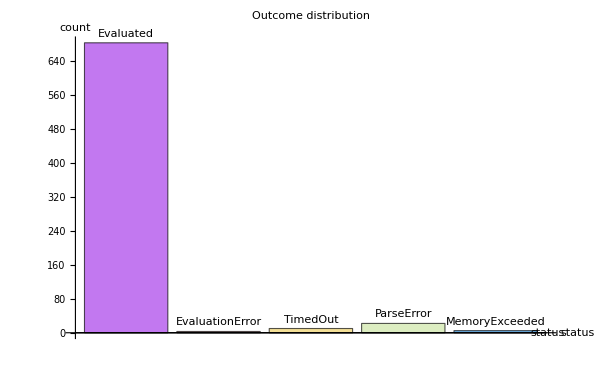

```mathematica
statusCounts = Counts[#["status"] & /@ run["results"]];
BarChart[statusCounts,
  ChartLabels -> Placed[Keys[statusCounts], Above],
  ChartStyle -> "Pastel",
  PlotLabel -> "Outcome distribution",
  ImageSize -> 600,
  AxesLabel -> {"status", "count"}]
```

## 9. Analysis — per-challenge grid

```mathematica
perChallenge = GroupBy[run["results"], #["challengeName"] &];
rows = KeyValueMap[
  Function[{name, rs},
    <|"challenge" -> name,
      "tests"     -> Length[rs],
      "passed"    -> Count[rs, _?(#["passed"] &)],
      "passRate"  -> N[Count[rs, _?(#["passed"] &)] / Length[rs]],
      "avgSec"    -> N[Mean[#["durationSec"] & /@ rs]],
      "statuses"  -> Counts[#["status"] & /@ rs]|>
  ],
  perChallenge
];
Dataset[SortBy[rows, -#["passRate"] &]]
```

## 10. Analysis — duration distribution

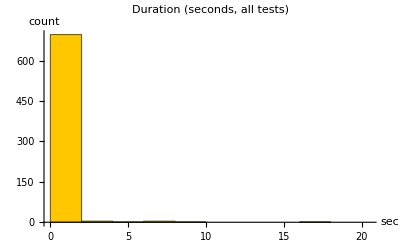
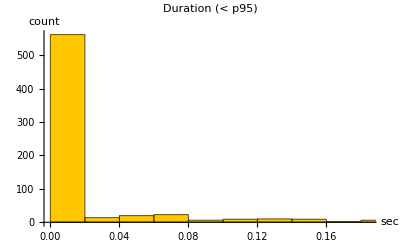

```mathematica
durations = #["durationSec"] & /@ run["results"];
Row[{
  Histogram[durations, 30,
    PlotLabel -> "Duration (seconds, all tests)",
    AxesLabel -> {"sec", "count"},
    ImageSize -> 400],
  Histogram[Select[durations, # < Quantile[durations, 0.95] &], 30,
    PlotLabel -> "Duration (< p95)",
    AxesLabel -> {"sec", "count"},
    ImageSize -> 400]
}]
```

```mathematica
Grid[{
  {"mean",    Mean[durations]},
  {"median",  Median[durations]},
  {"p90",     Quantile[durations, 0.90]},
  {"p95",     Quantile[durations, 0.95]},
  {"p99",     Quantile[durations, 0.99]},
  {"max",     Max[durations]}
}, Frame -> All, Alignment -> {{Left, Right}}]
```

mean | 1.30314
median | 0.00012
p90 | 0.14556
p95 | 0.593568
p99 | 60.004216
max | 60.136171

## 11. Analysis — slowest / fastest

```mathematica
slowest = Reverse @ SortBy[run["results"], #["durationSec"] &];
Dataset[
  Map[
    <|"testId" -> #["testId"],
      "status" -> #["status"],
      "passed" -> #["passed"],
      "durationSec" -> #["durationSec"]|> &,
    Take[slowest, UpTo[15]]
  ]
]
```

## 12. Analysis — failing-test inspector

Interactive drill-down into any failing test.

```mathematica
failing = Select[run["results"], ! #["passed"] &];
If[failing === {},
  "No failing tests.",
  Manipulate[
    Module[{r = failing[[i]]},
      Column[{
        Style[r["testId"], Bold, 16],
        Grid[{
          {"status",       r["status"]},
          {"error",        r["error"]},
          {"durationSec",  r["durationSec"]},
          {"messageCount", r["messageCount"]}
        }, Alignment -> {{Left, Left}}, Frame -> All],
        Pane[Column[{
          Style["expected", Bold],
          Short[r["expected"], 10],
          Style["actual",   Bold],
          Short[r["actualOutput"], 10]
        }], 700]
      }]
    ],
    {{i, 1, "failing test #"}, 1, Length[failing], 1}
  ]
]
```

## 13. Analysis — diff against a baseline

Set baselineDir to a previous runs/<runId> directory to compare.

```mathematica
baselineDir = FileNameJoin[{NotebookDirectory[], "runs", "INSERT-RUN-ID-HERE"}];

If[DirectoryQ[baselineDir],
  Module[{meta, res, base, diff},
    meta = Import[FileNameJoin[{baselineDir, "run.json"}], "RawJSON"];
    res  = Import[FileNameJoin[{baselineDir, "results.wxf"}], "WXF"];
    base = <|"runId" -> meta["runId"], "results" -> res|>;
    diff = ChallengesBenchmark`DiffRuns[base, run];
    Column[{
      Grid[{
        {"baseline",    diff["baseline"]},
        {"new",         diff["new"]},
        {"regressions", Length @ diff["regressions"]},
        {"fixes",       Length @ diff["fixes"]},
        {"newTests",    Length @ diff["newTests"]},
        {"missing",     Length @ diff["missingTests"]}
      }, Frame -> All, Alignment -> {{Left, Right}}],
      If[diff["regressions"] =!= {},
        Column[{Style["Regressions:", Bold],
                Column[diff["regressions"]]}],
        Style["No regressions.", Darker[Green]]
      ]
    }]
  ],
  Style["Edit baselineDir above to point at a previous run.", Italic]
]
```

Edit baselineDir above to point at a previous run.

## 14. Analysis — model comparison (optional)

Sweep every runs/<runId> in a directory and plot pass rates by model.

```mathematica
allRunDirs = FileNames["run-*", FileNameJoin[{NotebookDirectory[], "runs"}]];
allMetas = Quiet @ Map[
  Import[FileNameJoin[{#, "run.json"}], "RawJSON"] &,
  allRunDirs
];
modelRows = Select[allMetas, KeyExistsQ[#, "summary"] &];
Dataset[
  SortBy[
    Map[
      <|"runId"    -> #["runId"],
        "model"    -> #["model"],
        "finishedAt" -> Lookup[#, "finishedAt", "?"],
        "passed"   -> #["summary", "passed"],
        "total"    -> #["summary", "total"],
        "passRate" -> #["summary", "passRate"]|> &,
      modelRows
    ],
    -#["passRate"] &
  ]
]
```

```mathematica
If[Length[modelRows] > 0,
  BarChart[
    AssociationMap[#["summary", "passRate"] &, modelRows] /.
      (k_ -> v_) :> (k["model"] <> "/" <> StringTake[k["runId"], -6] -> v),
    ChartLabels -> Placed[Automatic, Above],
    PlotLabel -> "Pass rate by run",
    ImageSize -> 700,
    BarOrigin -> Left],
  "No runs found."
]
```

## Additional notes

Fix tests for Maximum Overhang Challenge

```mathematica
MaximumOverhang/1—Evaluated
Expected:1.0416666666666667
Actual:25/24
```